```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/analysis-mirror_neutrons/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## E-1

| Estimate | Standard Error | t-Statistic | P-Value
m | 2.5462×10^-7 | 1.56012×10^-6 | 0.163206 | 0.874404
c | 0.000701777 | 0.00700528 | 0.100178 | 0.922668

| DF | SS | MS
Model | 2 | 0.000244 | 0.000122
Error | 8 | 0.00119696 | 0.00014962
Uncorrected Total | 10 | 0.00144096 | 
Corrected Total | 9 | 0.00120095 |

1.00015

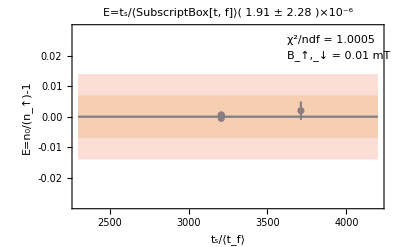

```mathematica
lvl3={};
tsadd=PlusMinus[11.306,0.397];
pttstfe={};fttstfe={};errtstfe={};
For[i=1,i≤dimdesc,i++,
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]&&descdat[[i]][[6]]==10)
,
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
xx=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe=AppendTo[pttstfe,{{xx[[1]],xx[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}}];
fttstfe=AppendTo[fttstfe,{xx[[1]],lvl3[[1]][[3]]}];
errtstfe=AppendTo[errtstfe,Sqrt[xx[[2]]^2+lvl3[[1]][[4]]^2]];
];
]
nlm=NonlinearModelFit[fttstfe,m x + c,{m,c},x,Weights->errtstfe];
ftval={m/.nlm["BestFitParameters"],c/.nlm["BestFitParameters"]};
fterr=nlm["ParameterErrors"];
ftresidue=nlm["FitResiduals"];
nlm["ParameterTable"]
nlm["ANOVATable"]
1+nlm["EstimatedVariance"]
Show[{
EDAListPlot[pttstfe,
PlotRange->{{2300,4200},{-.029,0.029}},Frame->True,FrameLabel->{"t_s/⟨t_f⟩","E=n_0/(n_↑)-1"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
PlotLabel->Style["E=t_s/⟨SubscriptBox[t, f]⟩( 1.91 ± 2.28 )×10^-6 ",Large],
Epilog->{
Text[Style["χ^2/ndf = 1.0005",FontSize->Large],{3900,.025}],
Text[Style["B_↑,_↓ = 0.01 mT",FontSize->Large],{3950,.02}]
}
],
Plot[{fterr[[1]],fterr[[1]]+fterr[[2]],fterr[[1]]-fterr[[2]],fterr[[1]]+2fterr[[2]],fterr[[1]]-2fterr[[2]]},{x,2300,4200},PlotStyle->{Gray,None,None,None,None},Filling->{{2->{3}},{4->{5}}}],
ListPlot[Table[{pttstfe[[k]][[1]],ftresidue[[k]]},{k,1,Dimensions[pttstfe][[1]]}],PlotMarkers->Style["✚",Medium],PlotStyle->Black]
}]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | -3.31491×10^-6 | 3.28992×10^-6 | -1.0076 | 0.3472
c | 0.0106538 | 0.0116321 | 0.915898 | 0.390182

| DF | SS | MS
Model | 2 | 0.0012883 | 0.000644148
Error | 7 | 0.00886506 | 0.00126644
Uncorrected Total | 9 | 0.0101534 | 
Corrected Total | 8 | 0.0101508 |

1.00127

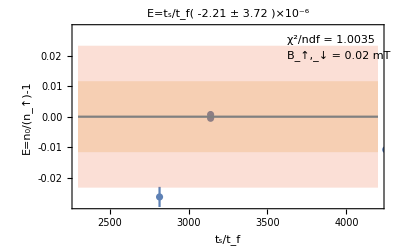

```mathematica
lvl3={};
tsadd=PlusMinus[11.306,0.397];
pttstfe={};fttstfe={};errtstfe={};
For[i=1,i≤dimdesc,i++,
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]&&descdat[[i]][[6]]==20)
,
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
xx=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe=AppendTo[pttstfe,{{xx[[1]],xx[[2]]},{lvl3[[1]][[3]],lvl3[[1]][[4]]}}];
fttstfe=AppendTo[fttstfe,{xx[[1]],lvl3[[1]][[3]]}];
errtstfe=AppendTo[errtstfe,Sqrt[xx[[2]]^2+lvl3[[1]][[4]]^2]];
];
]
nlm=NonlinearModelFit[fttstfe,m x + c,{m,c},x,Weights->errtstfe];
ftval={m/.nlm["BestFitParameters"],c/.nlm["BestFitParameters"]};
fterr=nlm["ParameterErrors"];
ftresidue=nlm["FitResiduals"];
(***)
nlm["ParameterTable"]
nlm["ANOVATable"]
1+nlm["EstimatedVariance"]
(***)
Show[{
EDAListPlot[pttstfe,
PlotRange->{{2300,4200},{-.029,0.029}},Frame->True,FrameLabel->{"t_s/t_f","E=n_0/(n_↑)-1"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
PlotLabel->Style["E=t_s/t_f( -2.21 ± 3.72 )×10^-6 ",Large],
Epilog->{
Text[Style["χ^2/ndf = 1.0035",FontSize->Large],{3900,.025}],
Text[Style["B_↑,_↓ = 0.02 mT",FontSize->Large],{3950,.02}]
}
],
Plot[{fterr[[1]],fterr[[1]]+fterr[[2]],fterr[[1]]-fterr[[2]],fterr[[1]]+2fterr[[2]],fterr[[1]]-2fterr[[2]]},{x,2300,4200},PlotStyle->{Gray,None,None,None,None},Filling->{{2->{3}},{4->{5}}}],
ListPlot[Table[{pttstfe[[k]][[1]],ftresidue[[k]]},{k,1,Dimensions[pttstfe][[1]]}],PlotMarkers->Style["✚",Medium],PlotStyle->Black]
}]
```

## A

| Estimate | Standard Error | t-Statistic | P-Value
m | -3.91237×10^-7 | 1.76669×10^-6 | -0.221452 | 0.830288
c | 0.000133519 | 0.0060341 | 0.0221274 | 0.982888

| DF | SS | MS
Model | 2 | 0.000411127 | 0.000205564
Error | 8 | 0.00281668 | 0.000352085
Uncorrected Total | 10 | 0.00322781 | 
Corrected Total | 9 | 0.00283395 |

1.00035

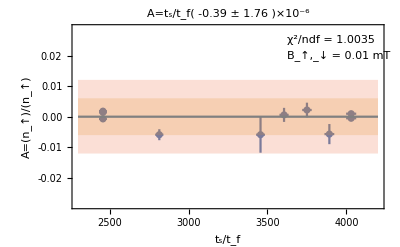

```mathematica
lvl3={};
tsadd=PlusMinus[11.306,0.397];
pttstfe={};fttstfe={};errtstfe={};
For[i=1,i≤dimdesc,i++,
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]&&descdat[[i]][[6]]==10)
,
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
xx=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe=AppendTo[pttstfe,{{xx[[1]],xx[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}}];
fttstfe=AppendTo[fttstfe,{xx[[1]],lvl3[[1]][[1]]}];
errtstfe=AppendTo[errtstfe,Sqrt[xx[[2]]^2+lvl3[[1]][[2]]^2]];
];
]
nlm=NonlinearModelFit[fttstfe,m x + c,{m,c},x,Weights->errtstfe];
ftval={m/.nlm["BestFitParameters"],c/.nlm["BestFitParameters"]};
fterr=nlm["ParameterErrors"];
ftresidue=nlm["FitResiduals"];
(***)
nlm["ParameterTable"]
nlm["ANOVATable"]
1+nlm["EstimatedVariance"]
(***)
Show[{
EDAListPlot[pttstfe,
PlotRange->{{2300,4200},{-.029,0.029}},Frame->True,FrameLabel->{"t_s/t_f","A=(n_↑)/(n_↑)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
PlotLabel->Style["A=t_s/t_f( -0.39 ± 1.76 )×10^-6 ",Large],
Epilog->{
Text[Style["χ^2/ndf = 1.0035",FontSize->Large],{3900,.025}],
Text[Style["B_↑,_↓ = 0.01 mT",FontSize->Large],{3950,.02}]
}
],
Plot[{fterr[[1]],fterr[[1]]+fterr[[2]],fterr[[1]]-fterr[[2]],fterr[[1]]+2fterr[[2]],fterr[[1]]-2fterr[[2]]},{x,2300,4200},PlotStyle->{Gray,None,None,None,None},Filling->{{2->{3}},{4->{5}}}],
ListPlot[Table[{pttstfe[[k]][[1]],ftresidue[[k]]},{k,1,Dimensions[pttstfe][[1]]}],PlotMarkers->Style["✚",Medium],PlotStyle->Black]
}]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | -3.98778×10^-7 | 1.22178×10^-6 | -0.326392 | 0.750856
c | -0.000297411 | 0.003706 | -0.0802512 | 0.937621

| DF | SS | MS
Model | 2 | 0.000597197 | 0.000298599
Error | 10 | 0.0038361 | 0.00038361
Uncorrected Total | 12 | 0.0044333 | 
Corrected Total | 11 | 0.00387697 |

1.00038

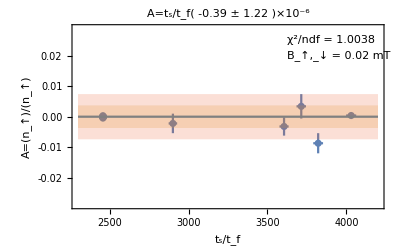

```mathematica
lvl3={};
tsadd=PlusMinus[11.306,0.397];
pttstfe={};fttstfe={};errtstfe={};
For[i=1,i≤dimdesc,i++,
If[(!MemberQ[{6,8,9,10,15,17,21,22,23,24,25,27,28,29,30,32,33,37},i]&&descdat[[i]][[6]]==20)
,
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
xx=(PlusMinus[descdat[[i]][[7]],.1]+tsadd)/PlusMinus[descdat[[i]][[9]],descdat[[i]][[10]]];
pttstfe=AppendTo[pttstfe,{{xx[[1]],xx[[2]]},{lvl3[[1]][[1]],lvl3[[1]][[2]]}}];
fttstfe=AppendTo[fttstfe,{xx[[1]],lvl3[[1]][[1]]}];
errtstfe=AppendTo[errtstfe,Sqrt[xx[[2]]^2+lvl3[[1]][[2]]^2]];
];
]
nlm=NonlinearModelFit[fttstfe,m x + c,{m,c},x,Weights->errtstfe];
ftval={m/.nlm["BestFitParameters"],c/.nlm["BestFitParameters"]};
fterr=nlm["ParameterErrors"];
ftresidue=nlm["FitResiduals"];
(***)
nlm["ParameterTable"]
nlm["ANOVATable"]
1+nlm["EstimatedVariance"]
(***)
Show[{
EDAListPlot[pttstfe,
PlotRange->{{2300,4200},{-.029,0.029}},Frame->True,FrameLabel->{"t_s/t_f","A=(n_↑)/(n_↑)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->36],LabelStyle->{36,Black,Bold},FrameTicksStyle->Bold,FrameStyle->Thickness[.004],ImageSize->{1000},
PlotLabel->Style["A=t_s/t_f( -0.39 ± 1.22 )×10^-6 ",Large],
Epilog->{
Text[Style["χ^2/ndf = 1.0038",FontSize->Large],{3900,.025}],
Text[Style["B_↑,_↓ = 0.02 mT",FontSize->Large],{3950,.02}]
}
],
Plot[{fterr[[1]],fterr[[1]]+fterr[[2]],fterr[[1]]-fterr[[2]],fterr[[1]]+2fterr[[2]],fterr[[1]]-2fterr[[2]]},{x,2300,4200},PlotStyle->{Gray,None,None,None,None},Filling->{{2->{3}},{4->{5}}}],
ListPlot[Table[{pttstfe[[k]][[1]],ftresidue[[k]]},{k,1,Dimensions[pttstfe][[1]]}],PlotMarkers->Style["✚",Medium],PlotStyle->Black]
}]
```